```mathematica
Get["/Users/kouamano/SCRIPT-MATHEMATICA/SCRIPTS/polar.txt"]
```

Get::noopen: "/Users/kouamano/SCRIPT-MATHEMATICA/SCRIPTS/polar.txt"を開くことができません．

$Failed

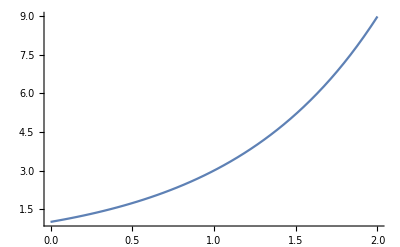

```mathematica
Plot[3^r,{r,0,2}]
```

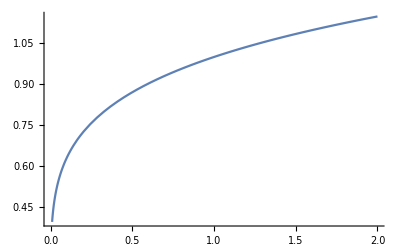

```mathematica
Plot[x^0.2,{x,0,2}]
```

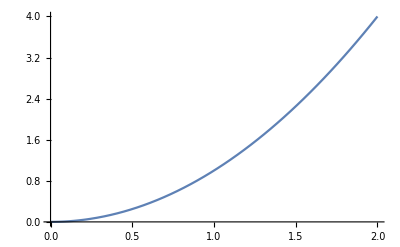

```mathematica
Plot[x^2,{x,0,2}]
```

```mathematica
averageDist[l_]:=Mean[Map[EuclideanDistance[#,Mean[l]]&,l]]
```

```mathematica
clusteringAdequationS[cl_]:=Tr[Map[Length[#]^(averageDist[#]/averageDist[Flatten[cl,1]])&,cl],Times]*Length[cl]
```

```mathematica
clusteringAdequationSI[cl_]:=Tr[Map[(1/Length[#])^(averageDist[#]/averageDist[Flatten[cl,1]])&,cl],Times]*Length[cl]
```

```mathematica
cl1={{{2,3},{2,3}},{{4,5}},{{3,3},{3,3},{3,3}}}
```

{{{2,3},{2,3}},{{4,5}},{{3,3},{3,3},{3,3}}}

```mathematica
clusteringAdequationS[cl1]//N
```

3.